```mathematica
p0 = 2
e1 = -0.55
e2 = -1.3
T = 310
k = 8.617*10^-5
β = 1/(k*T)
f[ϵ1_, ϵ2_]:=(P/p0 *(P/p0)^2*Exp[β * (2*ϵ1 - ϵ2) ])/(1 +(2*P)/p0 *(P/p0)^2*Exp[β * (2*ϵ1 - ϵ2)])
```

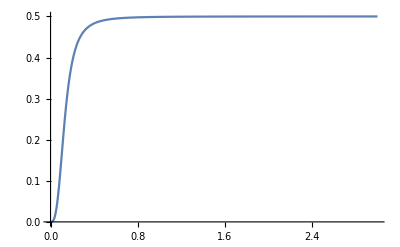

```mathematica
Plot[{f[ -0.55, -1.3]}, {P, 0, 3}, PlotRange-> All]
```